# EGGS Process

## Last Updated: 07/29/2023

```mathematica
(*Quit[];*)
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

```mathematica
(*todo: create import dataset function that puts otgehter all of "User Input" section*)
```

## General

## Values

```mathematica
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
mhz=1.*^6;
khz=1.*^3;
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
];
```

## Functions

### General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

### Dataset Processing

```mathematica
(*import already demodulated dataset*)
ProcessDataset[filename_]:=Module[
{
(*actual data*)
datasetRaw=Import[filename,{"/datasets/results"}],
(*parameters*)
(*modulationAmplitude=Import[filename,{"/datasets/modulation_amplitude_vpp"}],*)
(*processing*)
results,
carrierFreqMHz,
countThreshold
},

(*convert data to frequency, counts*)
results=Transpose[{
datasetRaw[[;;,1]]*ftwToFrequencyMHz,(*AOM/readout frequency, MHz*)
datasetRaw[[;;,4]]*1.*^-3,(*sideband frequency, kHz*)
datasetRaw[[;;,2]](*counts*)
}];

(*calculate values for processing*)
(*guess AOM/readout frequency*)
carrierFreqMHz=Mean[results[[;;,1]]];
(*find count threshold*)
countThreshold=FindThreshold[results[[;;,3]]];

(*process data*)
(*create copy of dataset and directly threshold counts into states*)
results[[;;,-1]]=1.-UnitStep[results[[;;,-1]]-countThreshold];
(*average states into probabilities*)
results=GroupBy[
results,
#[[;;2]]&,
N[Mean[#]]&
]//Values;

(*group by RSB/BSB*)
results=GroupBy[
results,
First[#]<carrierFreqMHz&
];
results={results[True],results[False]};
(*remove AOM/readout frequency and sort by x-axis*)
results=SortBy[#,First]&/@results[[;;,;;,2;;]];

(*clean up mess*)
Remove[datasetRaw];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

### Phonon Conversion

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];
```

## User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2023-08-06";
(*directoryString="/Users/claytonho/Documents/Research/Data & Analysis/EGGS";*)
(*directoryString="/Volumes/groups/motion/Data/2023-07-27";*)
```

```mathematica
(*select run*)
rid=26945;
```

## Process User Input

```mathematica
(*select file with give RID from all subdirectories*)
filenamesAll=FileNames["*.h5",directoryString,Infinity];
filenamesDJ=Select[filenamesAll,StringContainsQ[#,ToString[rid]]&];
```

```mathematica
(*just select dataset of interest as the first one that shows up that matches our RID*)
filenameDJ=First@filenamesDJ;
```

### Validate Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

```mathematica
(*check desired file exists*)
If[!FileExistsQ[filenameDJ],
MessageDialog["Failure :(\nError: Specified file not found ("<>filenameDJ<>")."];
FrontEndTokenExecute["EvaluatorAbort"]
];
```

```mathematica
(*(*check desired file is correct for processing*)
If[!StringContainsQ[filenamesDJ[[1]],"parametric",IgnoreCase->True],
MessageDialog["Failure :(\nError: Selected file incompatible with this Notebook.\nSelected file: "<>filenameDJ<>"."];
FrontEndTokenExecute["EvaluatorAbort"]
];*)
```

```mathematica
(*raise message dialog to let user know everything is OK*)
(*MessageDialog["Success!\nDesired file found: "<>filenameDJ];*)
```

## Process

## Preprocess

### Import

```mathematica
(*import and process data*)
dataset=ProcessDataset[filenameDJ];
```

```mathematica
(*get parameters*)
timeHeatSeconds=Import[filenameDJ,{"Attributes","/arguments"}]["time_eggs_heating_ms"]*1.*^-3;
timeReadoutSeconds=Import[filenameDJ,{"Attributes","/arguments"}]["time_readout_pipulse_us"]*1.*^-6;
```

```mathematica
(*tmp remove*)
(*timeHeatSeconds=0.005;*)
```

### Convert

```mathematica
(*separate data into more simple datasets*)
freqDataset=dataset[[1,;;,1]];
{rsbDataset,bsbDataset}=dataset;
```

```mathematica
(*process rsb/bsb ratio into observables*)
intensityRat=Transpose[{freqDataset,rsbDataset[[;;,2]]/bsbDataset[[;;,2]]}];
```

```mathematica
(*process data for coherent state*)
coherentDataset=intensityRat;
coherentDataset[[;;,2]]=CoherentC[coherentDataset[[;;,2]]];
```

```mathematica
(*process data for thermal state*)
thermalDataset=intensityRat;
thermalDataset[[;;,2]]=thermalDataset[[;;,2]]/(1.-thermalDataset[[;;,2]]);
```

## Fit

```mathematica
(*create sinc model for fitting*)
(*sincModel=α*(*(timeHeatSeconds*1000.)^2*)*Sinc[(π*timeHeatSeconds*1000.)*(x-β)+0.00001]^2+δ;*)
sincModel=α*Sinc[(π*timeHeatSeconds*1000.)*(x-β)+0.00001]^2+δ;
```

```mathematica
(*GuessSincParameters[dataset_]:=Module[
{offset=Median[dataset[[;;,2]]]},
Return[]
];*)
```

### Fit Sinc - RSB

```mathematica
(*guess sinc model fit params*)
{βRSBguess,αRSBguess}=rsbDataset[[First@Ordering[rsbDataset[[;;,2]],-1]]];
γRSBguess=timeHeatSeconds*1000;(*factor of 1000 is b/c x-axis is in kHz)*)
δRSBguess=Median[rsbDataset[[;;,2]]];
```

```mathematica
(*collate parameters*)
guessRSBSincFitParams={
αRSBguess-δRSBguess,(*α is rabi frequency;*)
1095(*βRSBguess*),(*β is resonance*)
(*γRSBguess*1(*scaleFactorDJ*),(*γ is evolution time*)*)
δRSBguess(*δ is offset*)
}
```

{0.0333333,1095,0.0333333}

```mathematica
(*constrain search range for parameters*)
sincRSBConstraints={
(*α>0,*)α<αRSBguess*3,
β>0.975*βRSBguess,β<1.025*βRSBguess
};
```

```mathematica
(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
AbsoluteTiming[
sincRSBFit=NonlinearModelFit[
rsbDataset,
(*Join[{sincModel,sincRSBConstraints}],*)
sincModel,
Transpose[{{α,β,(*γ,*)δ},guessRSBSincFitParams}],
x,
MaxIterations->10^3
];
]
```

{0.0014654,Null}

```mathematica
(*extract fit parameters*)
sincRSBFitValues=sincRSBFit["BestFitParameters"];
sincRSBFitFunction=sincRSBFit["BestFit"];
sincRSBFitConfidenceValues=sincRSBFit["ParameterConfidenceIntervalTableEntries"];
sincRSBFitTable=Style[sincRSBFit["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
α | 0.0193621 | 0.0170182 | {-0.0163917,0.055116}
β | 1095. | 0.205451 | {1094.57,1095.44}
δ | 0.032717 | 0.00428809 | {0.0237081,0.041726}

### Fit Sinc - BSB

```mathematica
(*guess sinc model fit params*)
δBSBguess=Median[bsbDataset[[;;,2]]];
bsbTMP=bsbDataset;
bsbTMP[[;;,2]]=Abs[bsbTMP[[;;,2]]-δBSBguess];
{βBSBguess,αBSBguess}=bsbTMP[[First@Ordering[bsbTMP[[;;,2]],-1]]];
(*factor of 1000 is b/c x-axis is in kHz)*)
γBSBguess=timeHeatSeconds*1000;
```

```mathematica
(*collate parameters*)
guessBSBSincFitParams={
αBSBguess-δBSBguess,(*α is rabi frequency;*)
1095,(*βBSBguess,*)(*β is resonance*)
(*γBSBguess*1(*scaleFactorDJ2*),(*γ is evolution time*)*)
δBSBguess(*δ is offset*)
}
```

{-0.7,1095,0.791667}

```mathematica
(*todo: check if rsb has good fit before trying to use its values*)
(*guessBSBSincFitParams={α,β,γ,δBSBguess}/.sincRSBFitValues;*)
```

```mathematica
(*constrain search range for parameters*)
sincBSBConstraints={
α<0,α<αBSBguess*3,
β>0.99*βBSBguess,β<1.01*βBSBguess
}
```

{α<0,α<0.275,β>1083.56,β<1105.45}

```mathematica
(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
sincModelBSB=sincModel;
AbsoluteTiming[
sincBSBFit=NonlinearModelFit[
bsbDataset,
Join[{sincModelBSB,sincBSBConstraints}],
Transpose[{{α,β,(*γ,*)δ},guessBSBSincFitParams}],
x,
MaxIterations->10^3
];
]
```

{0.0143883,Null}

```mathematica
(*extract fit parameters*)
sincBSBFitValues=sincBSBFit["BestFitParameters"];
sincBSBFitFunction=sincBSBFit["BestFit"];
sincBSBFitConfidenceValues=sincBSBFit["ParameterConfidenceIntervalTableEntries"];
sincBSBFitTable=Style[sincBSBFit["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
α | -0.00797549 | 0.028536 | {-0.0679274,0.0519764}
β | 1094.88 | 0.83632 | {1093.13,1096.64}
δ | 0.790427 | 0.00719033 | {0.775321,0.805534}

### Fit Ratio - Sinc

```mathematica
(*guess sinc model fit params*)
{βRatioguess,αRatioguess}=coherentDataset[[First@Ordering[coherentDataset[[;;,2]],-1]]];
γRatioguess=timeHeatSeconds*1000;(*factor of 1000 is b/c x-axis is in kHz)*)
δRatioguess=Median[coherentDataset[[;;,2]]];
(*combine guess params*)
guessRatioSincFitParams={
αRatioguess-δRatioguess,(*α is rabi frequency;*)
βRatioguess,(*β is resonance*)
(*γRatioguess*1(*scaleFactorDJ3*),(*γ is evolution time*)*)
δRatioguess(*δ is offset*)
};
```

```mathematica
(*constrain search range for parameters*)
sincRatioConstraints={
α>0,α<αRatioguess*3,
β>0.99*βRatioguess,β<1.01*βRatioguess
}
```

{α>0,α<0.248713,β>1082.57,β<1104.44}

```mathematica
(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
AbsoluteTiming[
sincRatioFit=NonlinearModelFit[
coherentDataset,
Join[{sincModel,sincRatioConstraints}],
Transpose[{{α,β,(*γ,*)δ},guessRatioSincFitParams}],
x,
MaxIterations->10^3
];
]
```

{0.0137193,Null}

```mathematica
(*extract fit parameters*)
sincRatioFitValues=sincRatioFit["BestFitParameters"];
sincRatioFitFunction=sincRatioFit["BestFit"];
sincRatioFitConfidenceValues=sincRatioFit["ParameterConfidenceIntervalTableEntries"];
sincRatioFitTable=Style[sincRatioFit["ParameterConfidenceIntervalTable"],Background->White];
```

## Process

```mathematica
(*divide fitted rsb/bsb and convert to coherent*)
fittedRatio=CoherentC[sincRSBFitFunction/sincBSBFitFunction];
```

```mathematica
(*calculate α*)
αFinalValue=CoherentC[Abs[(α/.sincRSBFitValues)/(α/.sincBSBFitValues)]];
```

InterpolatingFunction::dmval: Input value {2.4277} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
(*todo: divide fitted rsb/bsb and convert to thermal*)
```

## Plot

### RSB/BSB

```mathematica
(*plot raw RSB/BSB*)
rawPlot=ListPlot[
dataset,
PlotRange->{0.,1.},
Joined->{False,False},
FrameLabel->{ 
{Style["D-State Probability",{Black,Directive[15]}],None},
{Style["Tickle Frequency (kHz)",{Black,Directive[15]}],
Style["RSB vs BSB\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue}
];
```

```mathematica
(*plot sinc-fitted RSB*)
rsbFittedPlot=Plot[
sincRSBFitFunction,
{x,rsbDataset[[1,1]],rsbDataset[[-1,1]]},
PlotRange->Full,
PlotStyle->{Dashed,Red,Opacity[0.7]}
];
```

```mathematica
(*plot sinc-fitted BSB*)
bsbFittedPlot=Plot[
sincBSBFitFunction,
{x,bsbDataset[[1,1]],bsbDataset[[-1,1]]},
PlotRange->Full,
PlotStyle->{Dashed,Blue,Opacity[0.7]}
];
```

```mathematica
(*combine plots*)
sidebandPlot=Show[rawPlot,rsbFittedPlot,bsbFittedPlot];
```

```mathematica
(*create fitted sinc plots*)
fittedRatioPlot=Plot[
fittedRatio,
{x,freqDataset[[1]],freqDataset[[-1]]},
PlotRange->Full,
PlotStyle->{Dashed,Green,Thickness[0.004]},
PlotLegends->{"Fit RSB/Fit BSB"}
];
```

### Ratio

```mathematica
(*get max fitted function value to scale plots*)
maxSincRatioFitValue=sincRatioFitFunction/.{x->β/.sincRatioFitValues};
```

```mathematica
(*plot coherent state*)
coherentPlot=ListPlot[
coherentDataset,
PlotRange->{0.,Max[maxSincRatioFitValue,Max[coherentDataset[[;;,2]]]]*1.5},
Joined->False,
FrameLabel->{ 
{Style["α",{Black,Directive[15]}],None},
{Style["Tickle Frequency (kHz)",{Black,Directive[15]}],
Style["α^2 (RSB Fit/BSB Fit): "<>ToString[Round[αFinalValue,0.001]]<>"\nα^2 (Ratio Fit): "<>ToString[Round[α/.sincRatioFitValues,0.001]]<>" \nRID: "<>ToString[rid],{Black,Directive[15]}]}
}
];
```

```mathematica
(*create fitted sinc plots*)
coherentFittedPlot=Plot[
sincRatioFitFunction,
{x,coherentDataset[[1,1]],coherentDataset[[-1,1]]},
PlotRange->Full,
PlotStyle->{Dashed,Orange},
PlotLegends->{"Fitted Ratio"}
];
```

### Final Plot

```mathematica
(*combine plots*)
finalPlot=Show[coherentPlot,coherentFittedPlot,fittedRatioPlot];
```

## Show

{ | Estimate | Standard Error | Confidence Interval
α | 0.0193621 | 0.0170182 | {-0.0163917,0.055116}
β | 1095. | 0.205451 | {1094.57,1095.44}
δ | 0.032717 | 0.00428809 | {0.0237081,0.041726}, | Estimate | Standard Error | Confidence Interval
α | -0.00797549 | 0.028536 | {-0.0679274,0.0519764}
β | 1094.88 | 0.83632 | {1093.13,1096.64}
δ | 0.790427 | 0.00719033 | {0.775321,0.805534}, | Estimate | Standard Error | Confidence Interval
α | 0.0449095 | 0.0193511 | {0.00425435,0.0855647}
β | 1093.35 | 0.100962 | {1093.14,1093.56}
δ | 0.0399989 | 0.00487566 | {0.0297555,0.0502423}}

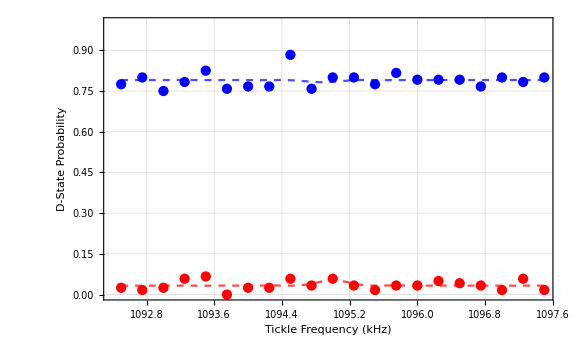

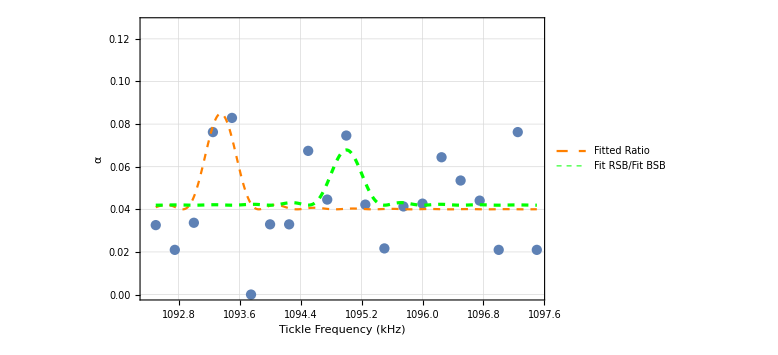

```mathematica
{sincRSBFitTable,
sincBSBFitTable,
sincRatioFitTable}
(*{sidebandPlot,finalPlot}*)
sidebandPlot
finalPlot
```

## Trends

## 100 dB

### Collate Data

```mathematica
x0100={0.1,0.2,0.3,0.4,0.5,1.,2.};
y1100={2.979,0.122,0.648,0.45,1.127,2.827,3.503};
y2100={0.076,0.065,0.464,0.628,1.328,1.208,1.015};
```

```mathematica
(*cherry pick data*)
data100=Transpose[{x0100,y1100}][[2;;6]];
(*data100=Transpose[{x0100,y2100}][[;;5]];*)
(*fit data*)
fit100=LinearModelFit[data100,{x^2},x,IncludeConstantBasis->False];
```

```mathematica
(*extract fit parameters*)
fit100Values=fit100["BestFitParameters"];
fit100Function=fit100["BestFit"];
fit100ConfidenceValues=fit100["ParameterConfidenceIntervalTableEntries"];
fit100Table=Style[fit100["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
x^2 | 2.95496 | 0.267245 | {2.21296,3.69695}

```mathematica
(*process heating magnitude*)
Ω100=Sqrt[fit100Values[[1]]];
```

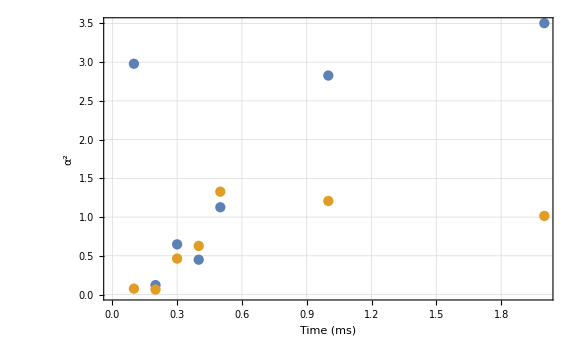

```mathematica
(*plot raw data*)
ListPlot[
{Transpose[{x0100,y1100}],
Transpose[{x0100,y2100}]},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["",{Black,Directive[15]}]}
}
]
```

### Fit & Plot

```mathematica
(*plot 100 dB data*)
data100Plot=ListPlot[
data100,
PlotRange->{{0,Automatic},Automatic},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["EGGS Calibration: 100 dB att\nΩ = "<>ToString[Round[Ω100,0.01]]<>" kHz",{Black,Directive[15]}]}
}
];
fit100Plot=Plot[
fit100Function,
{x,0,data100[[-1,1]]}
];
```

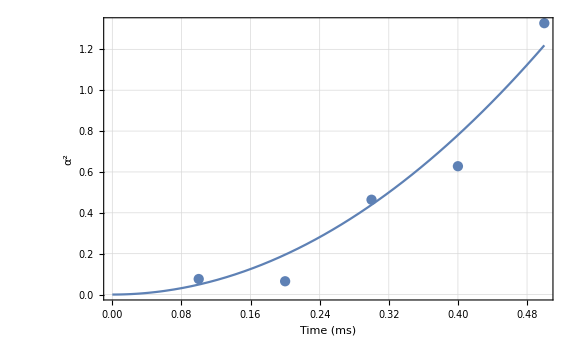

```mathematica
Show[data100Plot,fit100Plot]
```

## 110 dB

### Collate Data

```mathematica
(*collate raw data*)
x0110={0.5,0.75,1.,1.5,2.};
y1110={0.042,0.167,0.307,1.406,2.257};
y2110={0.015,0.146,0.335,1.02,1.233};
```

```mathematica
(*cherry pick data*)
data110=Transpose[{x0110,y1110}];
(*fit data*)
fit110=LinearModelFit[data110,{x^2},x,IncludeConstantBasis->False];
```

```mathematica
(*extract fit parameters*)
fit110Values=fit110["BestFitParameters"];
fit110Function=fit110["BestFit"];
fit110ConfidenceValues=fit110["ParameterConfidenceIntervalTableEntries"];
fit110Table=Style[fit110["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
x^2 | 0.561593 | 0.0361126 | {0.461328,0.661858}

```mathematica
(*process heating magnitude*)
Ω110=Sqrt[fit110Values[[1]]];
```

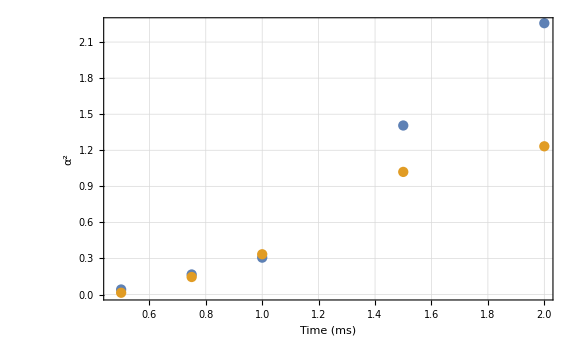

```mathematica
(*plot raw data*)
ListPlot[
{Transpose[{x0110,y1110}],
Transpose[{x0110,y2110}]},
PlotRange->{Automatic,Automatic},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["",{Black,Directive[15]}]}
}
]
```

### Fit & Plot

```mathematica
(*plot 110 dB data*)
data110Plot=ListPlot[
data110,
(*{Transpose[{x0110,y1110}],
Transpose[{x0110,y2110}]},*)
PlotRange->{{0,Automatic},Automatic},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["EGGS Calibration: 110 dB att\nΩ = "<>ToString[Round[Ω110,0.01]]<>" kHz",{Black,Directive[15]}]}
}
];
fit110Plot=Plot[
fit110Function,
{x,0,data110[[-1,1]]}
];
```

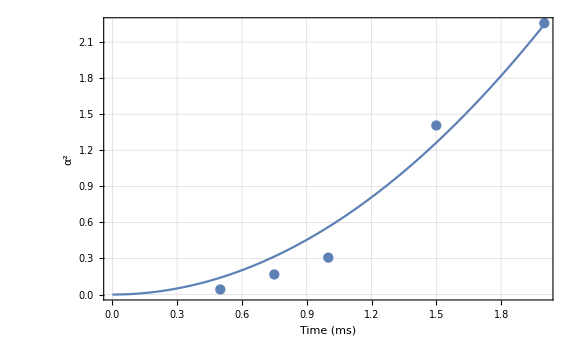

```mathematica
Show[data110Plot,fit110Plot]
```

## 120 dB

### Collate Data

```mathematica
x0120={1.,2.,5.,10.,20.,50.};
y1120={0.065,0.189,0.529,1.5,24.395,746.625};
y2120={0.006,0.077,0.338,0.403,0.326,0.817};
```

```mathematica
(*cherry pick data*)
data120=Transpose[{x0120,y1120}][[;;4]];
(*fit data*)
fit120=LinearModelFit[data120,{x^2},x,IncludeConstantBasis->False];
```

```mathematica
(*extract fit parameters*)
fit120Values=fit120["BestFitParameters"];
fit120Function=fit120["BestFit"];
fit120ConfidenceValues=fit120["ParameterConfidenceIntervalTableEntries"];
fit120Table=Style[fit120["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
x^2 | 0.015415 | 0.00113357 | {0.0118074,0.0190225}

```mathematica
(*process heating magnitude*)
Ω120=Sqrt[fit120Values[[1]]];
```

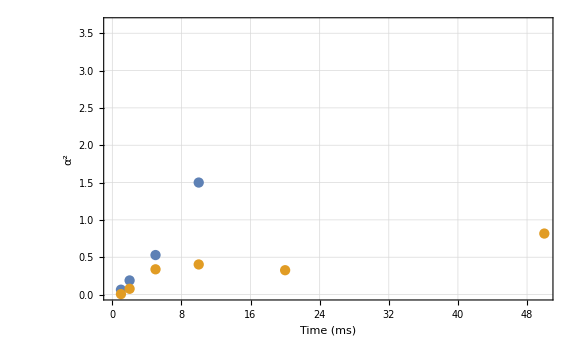

```mathematica
(*plot raw data*)
ListPlot[
{Transpose[{x0120,y1120}],
Transpose[{x0120,y2120}]},
PlotRange->{Automatic,Automatic},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["EGGS Calibration\n120 dB att",{Black,Directive[15]}]}
}
]
```

### Fit & Plot

```mathematica
(*plot 120 dB data*)
data120Plot=ListPlot[
data120,
PlotRange->{{0,Automatic},Automatic},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["EGGS Calibration: 120 dB att\nΩ = "<>ToString[Round[Ω120,0.01]]<>" kHz",{Black,Directive[15]}]}
}
];
fit120Plot=Plot[
fit120Function,
{x,0,data120[[-1,1]]}
];
```

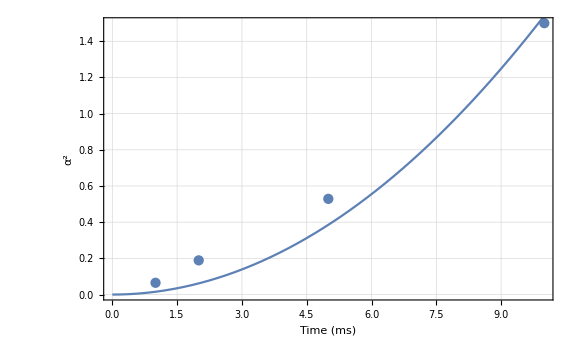

```mathematica
Show[data120Plot,fit120Plot]
```

## 130 dB

### Collate Data

```mathematica
x0130={1.,2.,5.,10.,20.,50.,100.};
y1130={0.252,6.982,0.189,0.216,3.938,0.959,3.877};
y2130={0.029,0.045,0.055,0.083,0.175,0.218,0.866};
```

```mathematica
(*cherry pick data*)
data130=Transpose[{x0130,y1130}][[{1,3,4,5,6,7}]];
(*fit data*)
fit130=LinearModelFit[data130,{x^2},x,IncludeConstantBasis->False];
```

```mathematica
(*extract fit parameters*)
fit130Values=fit130["BestFitParameters"];
fit130Function=fit130["BestFit"];
fit130ConfidenceValues=fit130["ParameterConfidenceIntervalTableEntries"];
fit130Table=Style[fit130["ParameterConfidenceIntervalTable"],Background->White]
```

| Estimate | Standard Error | Confidence Interval
x^2 | 0.000401889 | 0.000164598 | {-0.0000212241,0.000825002}

```mathematica
(*process heating magnitude*)
Ω130=Sqrt[fit130Values[[1]]];
```

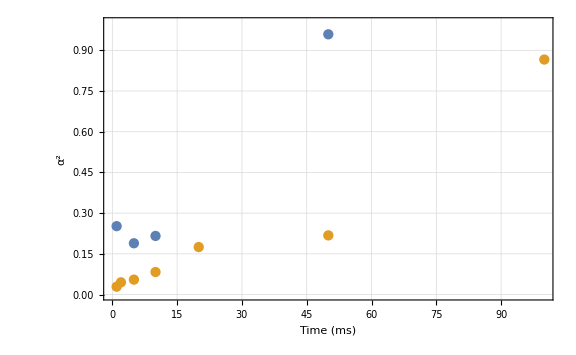

```mathematica
(*plot raw data*)
ListPlot[
{Transpose[{x0130,y1130}],
Transpose[{x0130,y2130}]},
(*PlotRange->{Automatic,{0,2.0}},*)
PlotRange->{Automatic,{0,1.0}},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["",{Black,Directive[15]}]}
}
]
```

### Fit & Plot

```mathematica
(*plot 130 dB data*)
data130Plot=ListPlot[
data130,
PlotRange->{{0,Automatic},Automatic},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["EGGS Calibration: 130 dB att\nΩ = "<>ToString[Round[Ω130,0.01]]<>" kHz",{Black,Directive[15]}]}
}
];
fit130Plot=Plot[
fit130Function,
{x,0,data130[[-1,1]]}
];
```

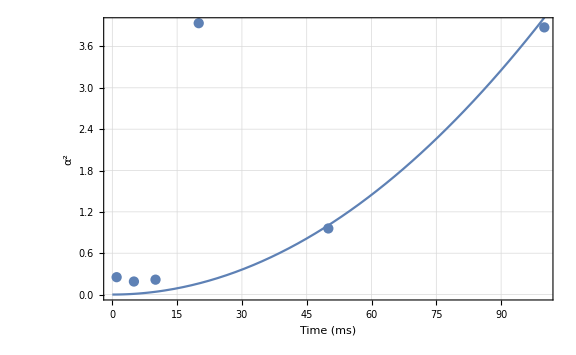

```mathematica
Show[data130Plot,fit130Plot]
```

## Summary

```mathematica
(*(*plot 130 dB data*)
data130Plot=ListPlot[
data130,
PlotRange->{{0,Automatic},Automatic},
FrameLabel->{ 
{Style["α^2",{Black,Directive[15]}],None},
{Style["Time (ms)",{Black,Directive[15]}],
Style["EGGS Calibration: 130 dB att\nΩ = "<>ToString[Round[Ω130,0.01]]<>" kHz",{Black,Directive[15]}]}
}
];
fit130Plot=Plot[
fit130Function,
{x,0,data130[[-1,1]]}
];*)
```

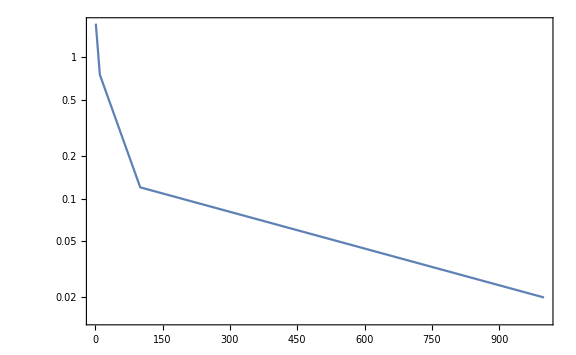

```mathematica
ListLogPlot[Transpose[{{1,10,100,1000},{1.72,0.75,0.12,0.02}}]]
```

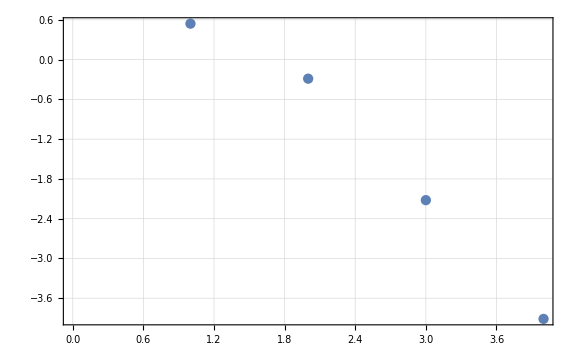

```mathematica
ListPlot[Log[{1.72,0.75,0.12,0.02}]]
```